### Training a Neural Network

```mathematica
1
```

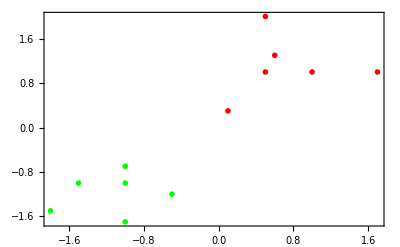

```mathematica
Plt=ListPlot[{{{-1.8,-1.5},{-1,-1.7},{-1.5,-1},{-1,-1},{-0.5,-1.2},{-1,-0.7}},{{1,1},{1.7,1},{0.5,2},{0.1,0.3},{0.5,1},{0.6,1.3}}},PlotMarkers->"OpenMarkers",Frame->True,PlotStyle->{Green,Red}]
```

```mathematica
2
```

```mathematica
Data={{-1.8,-1.5},{-1,-1.7},{-1.5,-1},{-1,-1},{-0.5,-1.2},{-1,-0.7},{1,1},{1.7,1},{0.5,2},{0.1,0.3},{0.5,1},{0.6,1.3}};
Target={-1,-1,-1,-1,-1,-1,1,1,1,1,1,1};
TrainData=MapThread[#1-> {#2}&,{Standardize[Data],Target},1];
```

3

```mathematica
Model=NetChain[{LinearLayer[1,"Input"-> 2],ElementwiseLayer[Ramp[#]&]}];
```

4

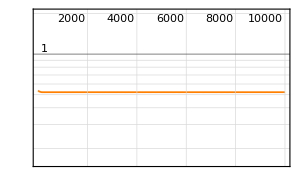
NetTrain Results
summary | ,,  batches:10000  rounds:10000  time:12s  examples/s:10179
data | ,,  training examples:12  processed examples:120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size12CPU
round | ,,  loss:5.22×10^-1
 | rounds
loss | -Graphics- | 
 |

```mathematica
Net=NetTrain[Model,TrainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64"]
```

5

```mathematica
TrainedNet1=Net["TrainedNet"]
```

NetChain[<>]

6

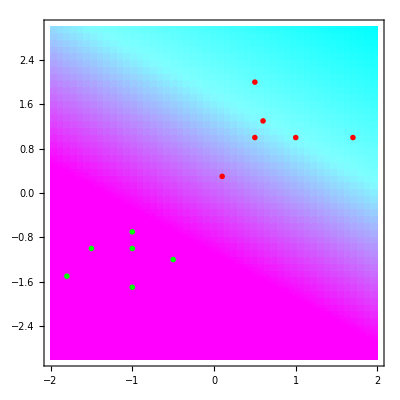

```mathematica
Show[DensityPlot[TrainedNet1[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],Plt]
```

```mathematica
7
```

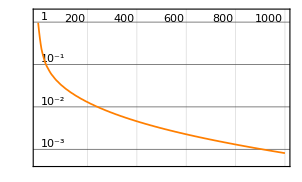
NetTrain Results
summary | ,,  batches:3000  rounds:1000  time:3.1s  examples/s:4791
data | ,,  training examples:12  processed examples:15000  skipped examples:0
method | ,,  ADAMoptimizer  batch size5CPU
round | ,,  loss:8.11×10^-4
 | rounds
loss | -Graphics- | 
 |

```mathematica
Net2=NetTrain[NetChain[{LinearLayer[1,"Input"-> 2],ElementwiseLayer[Tanh[#]&]}],TrainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64",LossFunction->MeanSquaredLossLayer[],BatchSize->5,MaxTrainingRounds->1000]
```

```mathematica
8
```

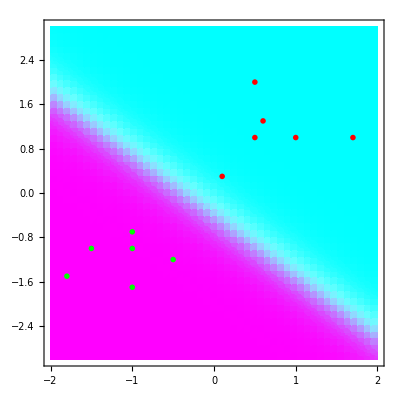

```mathematica
TrainedNet2=Net2["TrainedNet"];
Show[DensityPlot[TrainedNet2[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],Plt]
```

```mathematica
9
```

```mathematica
Dataset[{Association["LossPlot"-> Net2["LossPlot"]]}]
```

10

```mathematica
Net2["TrainingNet"]
```

NetGraph[<>]

```mathematica
11
```

```mathematica
Net2["Properties"]
```

{ArraysLearningRateMultipliers,BatchesPerRound,BatchLossList,BatchMeasurements,BatchMeasurementsLists,BatchSize,BestValidationRound,CheckpointingFiles,ExamplesProcessed,FinalLearningRate,FinalPlots,InitialLearningRate,InternalVersionNumber,LossPlot,MeanBatchesPerSecond,MeanExamplesPerSecond,NetTrainInputForm,OptimizationMethod,ReasonTrainingStopped,RoundLoss,RoundLossList,RoundMeasurements,RoundMeasurementsLists,RoundPositions,SkippedTrainingData,TargetDevice,TotalBatches,TotalRounds,TotalTrainingTime,TrainedNet,TrainingExamples,TrainingNet,TrainingUpdateSchedule,ValidationExamples,ValidationLoss,ValidationLossList,ValidationMeasurements,ValidationMeasurementsLists,ValidationPositions}

```mathematica
12
```

```mathematica
Net2["OptimizationMethod"]
```

{ADAM,Beta1→0.9,Beta2→0.999,Epsilon→1/100000,GradientClipping→None,L2Regularization→None,LearningRate→0.01,LearningRateSchedule→None,WeightClipping→None}

```mathematica
13
```

```mathematica
Net3=NetTrain[NetChain[{LinearLayer[1,"Input"-> 2],ElementwiseLayer["SoftSign"]}],TrainData,All,LearningRate->0.01,PerformanceGoal->"TrainingSpeed",TrainingProgressReporting->"Panel",TargetDevice->"CPU",RandomSeeding->88888,WorkingPrecision->"Real64",
Method->"ADAM" ,LossFunction->MeanSquaredLossLayer[],BatchSize->5,MaxTrainingRounds->1000,TrainingProgressMeasurements->{"MeanDeviation","MeanSquare","RSquared","StandardDeviation"} ]
```

NetTrain Results
summary | ,,  batches:3000  rounds:1000  time:3.9s  examples/s:3850
data | ,,  training examples:12  processed examples:15000  skipped examples:0
method | ,,  ADAMoptimizer  batch size5CPU
round | ,,  loss:2.25×10^-2  res. mean dev.:1.42×10^-1  res. mean sqr.:2.25×10^-2  res. r.b2:9.77×10^-1  res. s.d.:1.5×10^-1
 | 
 |

14

```mathematica
Net3[#]&/@{"RoundMeasurements"}//Dataset[#]&
```

15

```mathematica
Net3["FinalPlots"]//Dataset;
```

16

```mathematica
Measures=Net3[#]&/@{"RoundMeasurementsLists"};
Keys[Measures]
```

{{Loss,MeanDeviation,MeanSquare,RSquared,StandardDeviation}}

```mathematica
17
```

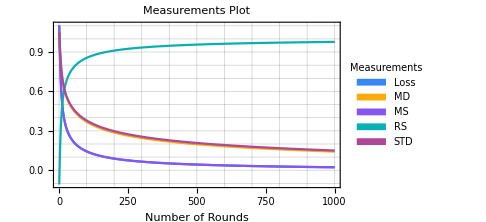
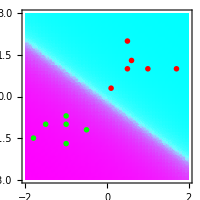
-Graphics- | -Graphics-

```mathematica
TrainedNet3=Net3["TrainedNet"];
Grid[{{ListLinePlot[{Measures[[1,1]](*Loss*),Measures[[1,2]](*MeanDeviation*),Measures[[1,3]](*MeanSquare*),Measures[[1,4]](*RSquared*),Measures[[1,5]](*StandardDeviation*)},PlotStyle->Table[ColorData[101,i],{i,1,5}],Frame->True,FrameLabel->{"Number of Rounds",None},PlotLabel->"Measurements Plot",GridLines->All,
PlotLegends->SwatchLegend[{Style["Loss",#],Style["MD",#],Style["MS",#],Style["RS",#],Style["STD",#]},LegendLabel->Style["Measurements",#],LegendFunction->(Framed[#,RoundingRadius->5,Background->LightGray]&)],ImageSize->Medium]&[Black],Show[DensityPlot[TrainedNet3[{x,y}],{x,-2,2},{y,-3,3},PlotPoints->50,ColorFunction->(RGBColor[1-#,2*#,1]&)],Plt,ImageSize-> 200]}}]
```

```mathematica
18
```

```mathematica
Export["C:\\Users\\lb-pc\\Desktop\\TrainedNet3.wlnet",Net3["TrainedNet"]]
```

C:\Users\lb-pc\Desktop\TrainedNet3.wlnet

```mathematica
19
```

```mathematica
Dataset@ AssociationMap[Import["C:\\Users\\lb-pc\\Desktop\\TrainedNet3.wlnet",#]&,{"Net","UninitializedNet","ArrayList","ArrayAssociation","WLVersion"}]
```

### Wolfram Neural net repository and

```mathematica
1
```

```mathematica
SystemOpen["https://resources.wolframcloud.com/NeuralNetRepository/"];
```

```mathematica
2
```

```mathematica
ResourceSearch[{"Name"-> "Image","ResourceType"->"NeuralNet"}]//Dataset[#,MaxItems->{4,3}]&
```

```mathematica
3
```

```mathematica
ResourceSearch[{"Name"-> "Wolfram ImageIdentify","ResourceType"-> "NeuralNet"},"Object"]
```

{ResourceObject[…]}

```mathematica
4
```

```mathematica
ResourceSearch[{"Name"-> "Wolfram ImageIdentify","ResourceType"-> "NeuralNet"},"Object"][[1]]//ResourceData
```

NetChain[<>]

5

```mathematica
Dataset[AssociationMap[ResourceObject["Wolfram ImageIdentify Net V1"][#]&,Map[ToString,{Name,RepositoryLocation,ResourceType,ContentElements,Version,Description,TrainingSetData,TrainingSetInformation,InputDomains,TaskType,Keywords,Attributes,LatestUpdate,DownloadedVersion,Format,ContributorInformation,DOI,Originator,ReleaseDate,ShortName,WolframLanguageVersionRequired},1]]]
```

### LeNet Neural Network

```mathematica
NetModel["LeNet Trained on MNIST Data",#]&/@{"Details","ShortName","TaskType","SourceMetadata"}//Column
```

This pioneer work for image classification with convolutional neural nets was released in 1998. It was developed by Yann LeCun and his collaborators at AT&T Labs while they experimented with a large range of machine learning solutions for classification on the MNIST dataset.
LeNet-Trained-on-MNIST-Data
{Classification}
<|Citation→Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998),Source→http://yann.lecun.com/exdb/lenet,Date→DateObject[{1998},Year,Gregorian,-5.]|>

```mathematica
7
```

```mathematica
NetModel["LeNet Trained on MNIST Data",#]&/@{"TrainingSetInformation","InputDomains","Performance"}//Column
```

MNIST Database of Handwritten Digits, consisting of 60,000 training and 10,000 test grayscale images of size 28x28.
{Image}
This model achieves 98.5% accuracy on the MNIST dataset.

```mathematica
8
```

```mathematica
(*This is for seven elements randomly sampled,but you can check the whole data set.*)
TableForm[
SeedRandom[900];
RandomSample[ResourceData["MNIST","TrainingData"],7],TableDirections->Row]
Map[ImageDimensions,%[[1;;7,1]]](*Test set : ResourceData["MNIST","TestData"] *)
```

-Graphics-→9 | -Graphics-→5 | -Graphics-→2 | -Graphics-→2 | -Graphics-→6 | -Graphics-→0 | -Graphics-→7

{{28,28},{28,28},{28,28},{28,28},{28,28},{28,28},{28,28}}

```mathematica
9
```

```mathematica
{TrainData,TestData}={ResourceData["MNIST","TrainingData"], ResourceData["MNIST","TestData"] };
```

```mathematica
10
```

```mathematica
UninitLeNet=NetModel["LeNet Trained on MNIST Data","UninitializedEvaluationNet"](*To work locally with the untrained model: NetModel["LeNet"]*)
```

NetChain[<>]

```mathematica
11
```

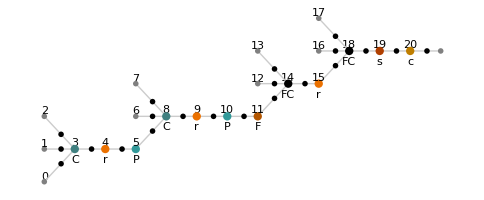

```mathematica
Information[UninitLeNet,"MXNetNodeGraphPlot"]
```

```mathematica
12
```

```mathematica
NetGraph[UninitLeNet]
```

NetGraph[<>]

```mathematica
13
```

```mathematica
{Enc=NetExtract[UninitLeNet,"Input"],Dec=NetExtract[UninitLeNet,"Output"]}//Row;
```

14

```mathematica
TestNet=NetInitialize[UninitLeNet,RandomSeeding->8888];
TestNet@TrainData[[1,1]](*TrainData[[1,1]] belongs to a zero*)
```

9

15

```mathematica
{net1,net2,net3,net4}=Table[NetInitialize[UninitLeNet,All,Method->i,RandomSeeding->8888],{i,{"Kaiming","Xavier","Orthogonal","Identity"}}];
{net1[TrainData[[1,1]]],net2[TrainData[[1,1]]],net3[TrainData[[1,1]]],net4[TrainData[[1,1]]]}
```

{9,9,5,3}

16

```mathematica
LeNet=NetInitialize[NetGraph[<|"LeNet NN"->UninitLeNet,"LeNet Loss"->CrossEntropyLossLayer@"Index"|>,{NetPort@"Input"->"LeNet NN","LeNet NN"->NetPort@{"LeNet Loss","Input"},NetPort@"Target"->NetPort@{"LeNet Loss","Target"}}],RandomSeeding->8888]
```

NetGraph[<>]

```mathematica
17
```

```mathematica
TrainDts=Dataset@Join[AssociationThread["Input"->#]& /@Keys[TrainData],AssociationThread["Target"-> #]&/@Values[TrainData]+1,2];
TestDts=Dataset@Join[AssociationThread["Input"->#]& /@Keys[TestData],AssociationThread["Target"-> #]&/@Values[TestData]+1,2];
```

```mathematica
18
```

```mathematica
BlockRandom[SeedRandom[999];
{RandomSample[TrainDts[[All]],4],RandomSample[TestDts[[All]],4]}]
```

{,}

```mathematica
19
```

```mathematica
NetResults=NetTrain[LeNet,TrainDts,All,ValidationSet->TestDts,MaxTrainingRounds->15,BatchSize->2096,LearningRate->Automatic,Method->"ADAM",TargetDevice->"CPU",PerformanceGoal->"TrainingMemory",WorkingPrecision->"Real32",RandomSeeding->99999,TrainingProgressMeasurements->{<|"Measurement"->"Accuracy","ClassAveraging"->"Macro"|>,
<|"Measurement"->"Precision","ClassAveraging"->"Macro"|>
,<|"Measurement"->"F1Score","ClassAveraging"->"Macro"|>
,<|"Measurement"->"Recall","ClassAveraging"->"Macro"|>
,<|"Measurement"->"ROCCurvePlot","ClassAveraging"->"Macro"|>
,<|"Measurement"->"ConfusionMatrixPlot","ClassAveraging"->"Macro"|>
},TrainingStoppingCriterion-> <|"Criterion"->"Loss","AbsoluteChange"->0.001|>]
```

NetTrain Results
summary | ,,  batches:348  rounds:12  time:14min  examples/s:850
data | ,,  training examples:60000  validation examples:10000  processed examples:729408  skipped examples:0
method | ,,  ADAMoptimizer  batch size2096CPU
round | ,,  loss:3.08×10^-2  acc.:99.102%  prec.:99.095%  F1:99.094%  recall:99.093%
validation | ,,  loss:3.85×10^-2  acc.:98.79%  prec.:98.79%  F1:98.78%  recall:98.78%
 | 
-Graphics-  training set	-Graphics-  validation set |

```mathematica
20
```

```mathematica
NetExtract[NetResults["TrainedNet"],"LeNet NN"];
TrainedLeNet=NetReplacePart[%,{"Input"->Enc,"Output"->Dec}];
```

NetChain[<>]

```mathematica
21
```

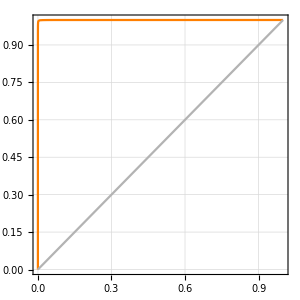
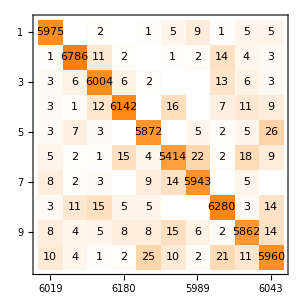
RoundMeasurements | ROCCurvePlot | ConfusionMatrixPlot
 | recall | -Graphics-
 | false positive rate | actual class | -Graphics-
 | predicted class

```mathematica
NetResults["RoundMeasurements"][[1;;5]];
Normal[NetResults["RoundMeasurements"][[6;;7]]];
Grid[{{Style["RoundMeasurements",#1,#2],Style[%[[1,1]],#1,#2],Style[%[[2,1]],#1,#2]},{Dataset[%%],%[[1,2]],%[[2,2]]}},Dividers->Center]&[Bold,FontFamily->"Alegreya SC"]
```

22

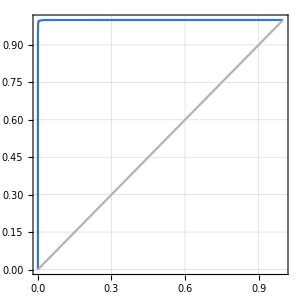
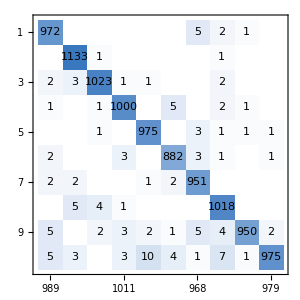
ValidationMeasurements | ROCCurvePlot | ConfusionMatrixPlot
 | recall | -Graphics-
 | false positive rate | actual class | -Graphics-
 | predicted class

```mathematica
NetResults["ValidationMeasurements"][[1;;5]];
Normal[NetResults["ValidationMeasurements"][[6;;7]]];
Grid[{{Style["ValidationMeasurements",#1,#2],Style[%[[1,1]],#1,#2],Style[%[[2,1]],#1,#2]},{Dataset[%%],%[[1,2]],%[[2,2]]}},Dividers->Center]&[Bold,FontFamily->"Alegreya SC"]
```

23

```mathematica
Expls=Keys[{TestData[[2150]],TestData[[3910]],TestData[[6115]],TestData[[6011]],TestData[[7834]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

24

```mathematica
TrainedLeNet[Expls,"TopProbabilities"]
```

{{2→0.998171},{3→0.999922},{6→0.587542,0→0.404588},{6→0.971103},{7→0.99937}}

```mathematica
25
```

```mathematica
TableForm[Transpose@{TrainedLeNet[ Expls,{"TopDecisions",2}],TrainedLeNet[ Expls,{"TopProbabilities",2}]},TableHeadings->{Map[ToString,{2,3,6,5,7},1],{"Top Decisions","Top Probabilities "}},TableAlignments->Center]
```

| Top Decisions | Top Probabilities 
2 | 3
2 | 3→0.00165948
2→0.998171
3 | 9
3 | 9→0.0000534744
3→0.999922
6 | 0
6 | 0→0.404588
6→0.587542
5 | 0
6 | 0→0.0140468
6→0.971103
7 | 3
7 | 3→0.000526736
7→0.99937

```mathematica
26
```

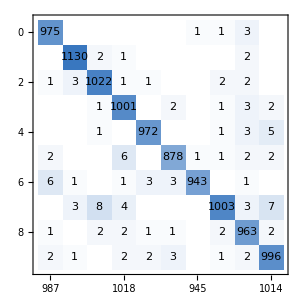
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[TrainedLeNet,TestData,"ConfusionMatrixPlot"]
```